```mathematica
(*   potenzialesingolacarica[q_,x1_,y1_,x_,y_]= q/Sqrt[(x-x1)^2 + (y-y1)^2];
caricasingola {q,x,y};
cariche lista di terne{ {q1,x1,y1} , {q2,x2,y2} , {q3,x3,y3}    .... }


*)
```

```mathematica
pot[cariche_,  x_, y_] :=Sum[  
r= Sqrt[ (cariche[[i,2]] - x)^2 + (cariche[[i,3]] - y)^2   ];   (*r variabile temporanea*)
		    cariche[[i,1]]/r,                   (*   addendo, ultimo elemento prima della lista su dove cicla*)
                      {i,1,Length[cariche]} 
                                                        ];

es31={ {1,-3,-3} , {1,1,1} };
es32={ {1,-3,-3} , {-1,1,1} };
es33={ {1,-3,-3} , {1,-2.7,-2.7} };

gra311=Plot3D[Evaluate[ pot[ es31,x,y]], {x,-5,5},{y,-5,5}];
gra312=ContourPlot[Evaluate[ pot[ es31,x,y]], {x,-5,5},{y,-5,5}];

gra321=Plot3D[Evaluate[ pot[ es32,x,y]], {x,-5,5},{y,-5,5}];
gra322=ContourPlot[Evaluate[ pot[ es32,x,y]], {x,-5,5},{y,-5,5}];

gra331=Plot3D[Evaluate[ pot[ es33,x,y]], {x,-5,5},{y,-5,5}];
gra332=ContourPlot[Evaluate[ pot[ es33,x,y]], {x,-5,5},{y,-5,5}];



campoelettrico[cariche_,x_,y_]:={ -D[pot[cariche,a,b],a] , -D[pot[cariche,a,b],b]}/.{a->x , b->y } ;

disegnacampo[ {xmin_,xmax_},{ymin_,ymax_}, cariche_] := Show[ Graphics[   

Table[ 
   sizex=(xmax-xmin)/15;
   sizey=(ymax-ymin)/15;
 xi= xmin+sizex*(i-0.5);
 yj= ymin+sizey*(j-0.5);  (*sono al centro di ogni quadratino*)

campo=campoelettrico[ cariche,xi,yj ];  (*campo in ogni punto*)
norma = Sqrt[campo.campo];    (*normalizzo le frecce*)
freccia=Arrow[ {{xi,yj} ,{xi,yj} + campo/norma}];  (*non banali operazioni tra liste    +  ,  .  ,  /    *) 
        freccia,           (*elemento generico*)
{i,1,15},{j,1,15}
       ]
                                                                                                                                                     ]
      ];



??Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive that represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.

Attributes[Arrow]={Protected,ReadProtected}

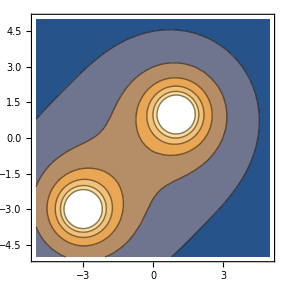
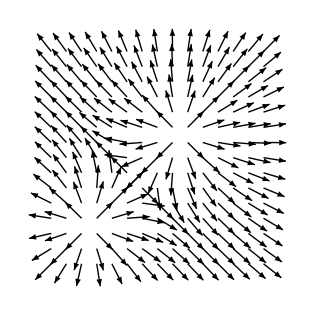
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
{gra311,gra312,disegnacampo[{-5,5},{-5,5} , es31]}
```

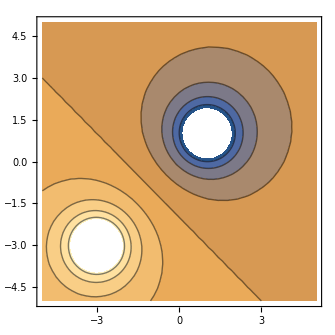
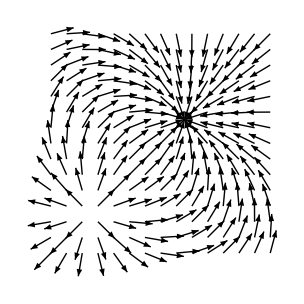
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
{gra321,gra322,disegnacampo[{-5,5},{-5,5} , es32]}
```

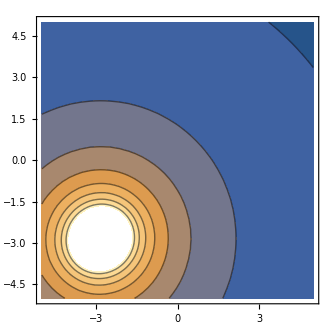
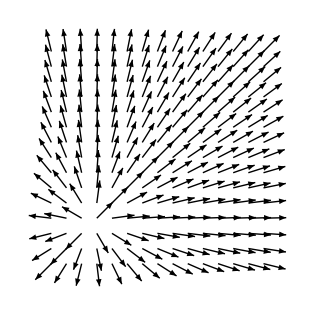
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
{gra331,gra332,disegnacampo[{-5,5},{-5,5} , es33]}
```